# Building WolframCloud APIs for JavaScript (React, Node, AWS) Livecoding Session 2

## Overview

Assumptions:
- Familiarity with Mathematica.  
- Familiarity of JS is helpful but not required for this presentation.

A few words about:
- Introduction and background for React (https://reactjs.org/) / Axios and Node (https://nodejs.org/en/) / Express.
- Wolfram setup, we will use the following tools:
	- Mathematica desktop (wolfram.com/) & Wolfram Cloud (wolframcloud.com - free sign up.  You can use Wolfram Cloud (WC) alone if you like)
- Other than Wolfram setup:
	- npm (https://www.npmjs.com/) 
	- git (https://git-scm.com/)
	- GitHub (https://github.com/)
	- AWS (free tier: https://aws.amazon.com/console/)
	- AWS-CLI (https://aws.amazon.com/cli/)
	- AWS Amplify (https://aws.amazon.com/amplify/)
	- create-react-app (https://facebook.github.io/create-react-app/)
	- Chrome browser (google.com/chrome).  We will use chrome developer tools.  Other browsers and their browser tools may not be sufficient for what we will doing)
	- Postman (getpostman.com/ for validating and testing APIs)

## Introduction

Motivating principle: separation of duties for people and software supporting the goals of modular design principles.  Easy to understand separating people by expertise in front-end, back-end and quantitative capabilities and code production.

This is the first of three (or more) live-coding walk-through’s that show an approach to integrating Mathematica to a browser front-end (ReactJS) and a serverless back-end (Node JS and AWS).

ReactJS is a JavaScript (JS) library widely used to make single page applications (SPAs).   ‘Hooks’ were introduced in the recently released version 16.8 (https://reactjs.org/docs/hooks-intro.html).  Using hooks allows React developers to write JS applications using 100% functional methods - eliminating the need for JS classes.  There are many advantages to this new capability and we will focus on the implications for APIs between React and the Wolfram Cloud (WC) and between AWS and WC.

We will show JS and JSX (https://reactjs.org/docs/introducing-jsx.html) with respect to how the API requests (req) and responses (res) are managed.  The JS browser app is a bear bones deployment with minimal styling and organization considerations.  

We will iterate from the simplest possible API (that I can think of) to ever more complex patterns.  There are JS and React considerations that impact the WC side of the API.  A number of these considerations will be presented, discussed and dealt with.  In every instance the goal is to produce Mathematica side code that is simultaneously used for presentation in a browser and analytical use is Mathematica. 

Some requests and considerations:
- You will see the URL I use (my WC account) and API end-points I am using.  I've made these public for these live coding sessions.  It's ok during the live coding session to use my APIs if you can't make yours work, but please setup your own WC account, make your own APIs and use them.

The general development pattern:
1.0) Three parts to APIFunction[...]:
	1.1) inputs
	1.2) functions
	1.3) output format
2.0) Test by passing an association of API inputs <|key -> value, ...|>
3.0) Two’ish parts to CloudDeploy[...]:
	3.1) the api function (1 above)
	3.2) options:
		3.2.1) the path and api name
		3.2.2) permissions
4.0) Test:
	4.1) to a browser with StartWebSession[...] and WebExecute[...]
	4.2) to postman
5.0) Connect to:
	5.1) front-end (React)
	5.2) backend (Node)
		5.2.1) test serverless api between AWS (via Node) and WC 

Here are a couple web sites that are built on this pattern where the front-end is a Single Page Application (SPA) using React, the back-end is serverless and built on NodeJS - AWS, and everything computational is done with Wolfram (Wolfram Cloud):
	- https://www.aitoconsulting.org/options-pub
	- https://www.christyhealth.org/

## API-5) JSON: more complicated structures from external sources

#### get data from outside MM

A good source of semi structured JSON for development and testing is https://jsonplaceholder.typicode.com
{ posts, comments, albums, photos, todos, users }

Note the different import results given the use of “JSON” or “RawJSON”.

```mathematica
Import["https://jsonplaceholder.typicode.com/users","JSON"][[1;;3]]
```

{{id→1,name→Leanne Graham,username→Bret,email→Sincere@april.biz,address→{street→Kulas Light,suite→Apt. 556,city→Gwenborough,zipcode→92998-3874,geo→{lat→-37.3159,lng→81.1496}},phone→1-770-736-8031 x56442,website→hildegard.org,company→{name→Romaguera-Crona,catchPhrase→Multi-layered client-server neural-net,bs→harness real-time e-markets}},{id→2,name→Ervin Howell,username→Antonette,email→Shanna@melissa.tv,address→{street→Victor Plains,suite→Suite 879,city→Wisokyburgh,zipcode→90566-7771,geo→{lat→-43.9509,lng→-34.4618}},phone→010-692-6593 x09125,website→anastasia.net,company→{name→Deckow-Crist,catchPhrase→Proactive didactic contingency,bs→synergize scalable supply-chains}},{id→3,name→Clementine Bauch,username→Samantha,email→Nathan@yesenia.net,address→{street→Douglas Extension,suite→Suite 847,city→McKenziehaven,zipcode→59590-4157,geo→{lat→-68.6102,lng→-47.0653}},phone→1-463-123-4447,website→ramiro.info,company→{name→Romaguera-Jacobson,catchPhrase→Face to face bifurcated interface,bs→e-enable strategic applications}}}

```mathematica
Import["https://jsonplaceholder.typicode.com/users","RawJSON"][[1;;3]]
%//Dataset
```

{<|id→1,name→Leanne Graham,username→Bret,email→Sincere@april.biz,address→<|street→Kulas Light,suite→Apt. 556,city→Gwenborough,zipcode→92998-3874,geo→<|lat→-37.3159,lng→81.1496|>|>,phone→1-770-736-8031 x56442,website→hildegard.org,company→<|name→Romaguera-Crona,catchPhrase→Multi-layered client-server neural-net,bs→harness real-time e-markets|>|>,<|id→2,name→Ervin Howell,username→Antonette,email→Shanna@melissa.tv,address→<|street→Victor Plains,suite→Suite 879,city→Wisokyburgh,zipcode→90566-7771,geo→<|lat→-43.9509,lng→-34.4618|>|>,phone→010-692-6593 x09125,website→anastasia.net,company→<|name→Deckow-Crist,catchPhrase→Proactive didactic contingency,bs→synergize scalable supply-chains|>|>,<|id→3,name→Clementine Bauch,username→Samantha,email→Nathan@yesenia.net,address→<|street→Douglas Extension,suite→Suite 847,city→McKenziehaven,zipcode→59590-4157,geo→<|lat→-68.6102,lng→-47.0653|>|>,phone→1-463-123-4447,website→ramiro.info,company→<|name→Romaguera-Jacobson,catchPhrase→Face to face bifurcated interface,bs→e-enable strategic applications|>|>}

Dataset[<>]

```mathematica
ClearAll[choices,get]
choices=Sort[{"posts","comments","albums","photos","todos","users"}]
get[it_String]:=Import["https://jsonplaceholder.typicode.com/"<>it,"RawJSON"]
```

{albums,comments,photos,posts,todos,users}

```mathematica
get["users"]//Dataset
```

Dataset[<>]

```mathematica
Dataset[get["users"]][RandomSample[#,3]&][SortBy[#,"id"]&][All,{{"id","name"},Query["address","geo"]}/*Apply[Join]]
%//Normal
```

Dataset[<>]

{<|id→4,name→Patricia Lebsack,lat→29.4572,lng→-164.2990|>,<|id→5,name→Chelsey Dietrich,lat→-31.8129,lng→62.5342|>,<|id→10,name→Clementina DuBuque,lat→-38.2386,lng→57.2232|>}

Illustration of various ways to query data from the dataset.

#### building an API that makes a call to an external endpoint for data needed by the API.

This breaks with #n

```mathematica
Dataset[get["users"]][RandomSample[#,3]&][SortBy[#,"id"]&][All,{{"id","name"},Query["address","geo"]}/*Apply[Join]]
```

Dataset[<>]

This works with #n

```mathematica
Dataset[SortBy[RandomSample[get["users"],3],"id"]][All,{{"id","name"},Query["address","geo"]}/*Apply[Join]]
```

Dataset[<>]

```mathematica
ClearAll[api]
api= APIFunction[
{
"it"->"String",
"n"->"Integer"
},
Function[
Dataset[SortBy[RandomSample[get["users"],#n],"id"]][All,{{"id","name"},Query["address","geo"]}/*Apply[Join]]//Normal
],
 "JSON"
];

api[<|"it"->"users","n"->4|>]
%//Dataset
```

{<|id→3,name→Clementine Bauch,lat→-68.6102,lng→-47.0653|>,<|id→4,name→Patricia Lebsack,lat→29.4572,lng→-164.2990|>,<|id→7,name→Kurtis Weissnat,lat→24.8918,lng→21.8984|>,<|id→9,name→Glenna Reichert,lat→24.6463,lng→-168.8889|>}

Dataset[<>]

```mathematica
ClearAll[cd]
cd=CloudDeploy[
api,
"/live-coding/placeholder/",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/placeholder]

```mathematica
ClearAll[url,session]
url=URLBuild[cd,<|"it"->"users","n"->4|>]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/placeholder?it=users&n=4

We can send the whole dataset to the front-end and let the front-end guys figure it out, or set up controls in the front-end and send from the quant API only what is wanted.  This later approach is like GraphQL; query only what you want and minimize the quantity of data being transported via HTTP.

## API-6) Compute word counts

```mathematica
Dataset[ get["posts"] ]
```

Dataset[<>]

Requirement: WordCount[ ] all the words in the body of posts.

Start with...

```mathematica
Dataset[ get["posts"] ][All,{"body"}]
```

Dataset[<>]

```mathematica
Dataset[ get["posts"] ][Union,"body",Head]
```

Finish with...

```mathematica
<|"word"->#[[1]],"count"->#[[2]]|>&/@Transpose[ Normal[ Dataset[ get["posts"] ][StringJoin/*WordCounts/*Sort/*Reverse/*Query[{Keys,Values}],"body"] ] ]//Short
```

{<|word→et,count→109|>,«279»,<|word→quiacupiditate,count→1|>}

```mathematica
Take[
<|"word"->#[[1]],"count"->#[[2]]|>&/@(Dataset[ get["posts"] ][All,"body"]//Normal//StringJoin//WordCounts//Sort//Reverse//Query[{Keys,Values}]//Transpose),
10]
```

{<|word→et,count→109|>,<|word→qui,count→57|>,<|word→aut,count→56|>,<|word→ut,count→49|>,<|word→est,count→39|>,<|word→quia,count→36|>,<|word→voluptatem,count→35|>,<|word→molestiae,count→33|>,<|word→rerum,count→31|>,<|word→omnis,count→30|>}

#### build word count API

```mathematica
ClearAll[api]
api= APIFunction[
{
"part"->"String",
"n"->"Integer"
},
Function[
Take[
<|"word"->#[[1]],"count"->#[[2]]|>&/@Transpose[ Normal[ Dataset[ get["posts"] ][StringJoin/*WordCounts/*Sort/*Reverse/*Query[{Keys,Values}],#part] ] ],
#n]
],
 "JSON"
];
api[<|"part"->"body","n"->10|>]
%//Dataset
```

{<|word→et,count→109|>,<|word→qui,count→57|>,<|word→aut,count→56|>,<|word→ut,count→49|>,<|word→est,count→39|>,<|word→quia,count→36|>,<|word→voluptatem,count→35|>,<|word→molestiae,count→33|>,<|word→rerum,count→31|>,<|word→omnis,count→30|>}

Dataset[<>]

```mathematica
ClearAll[cd]
cd=CloudDeploy[
api,
"/live-coding/wordcount/",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/wordcount]

```mathematica
ClearAll[url,session]
url=URLBuild[cd,<|"part"->"body","n"->10|>]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/wordcount?part=body&n=10

Let’s step back for a minute

- We develop with Dataset[]’s in MM such that when normalized (Normal@Dataset[...]) they can be used directly as JSON API endpoint results!  (See Al Calvitti and Andreas Lauschke live-coding sessions and Al Calvitti upcoming book  to get more ideas about how far this can go.)
- We can be computationally imaginative and efficient in MM taking our MM work to the API end point for hand-off to the front-end and back-end guys.
- We can separate work and responsibilities within an organization with transparent hand-off points.
- We comply with separation of duties (and responsibilities)
- We separate the project plan tasking timelines because can stub the handoffs and let each group build as they can and as they need filling in the stubs when ready.  This eases project dependence pressures and hence the risk of project stalling roadblocks

## API-7) Put data to & Get data from WC

It’s possible to use WC as a data repository.  We show how this can be done.  First find your CloudBase, make sure this is right for you.

```mathematica
$CloudBase
```

https://www.wolframcloud.com/

Open the URL and sign in.  Click the ‘Cloud Files’ link.  This is where we will store our data.

```mathematica
ClearAll[todoDS]
todoDS=Dataset[get["todos"]]
```

Dataset[<>]

CloudPut the dataset to a location in your Wolfram Cloud.

```mathematica
CloudPut[todoDS,CloudObject["data/todos",Permissions->"Public"]]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/data/todos]

```mathematica
ClearAll[todoDS]
todoDS=CloudGet["data/todos"]
```

Dataset[<>]

We’ve seen how to put data to and get data from WC.  Now let’s combine this into our API processing capabilities.  

The API will get the todo list, and return some number, n, of todos that are completed or not.  Let’s work through the steps before we build the API.

```mathematica
temp=CloudGet["data/todos"]
```

Dataset[<>]

What are Head[ ]’s?  Any unexpected String[ ]’s or Missing[ ]’s?

```mathematica
temp[Union,All,Head]
```

Dataset[<>]

There are a number of ways we can go.  The API request will give us 2 selection criteria: competed {True or False}, and the number of to do’s to return.  We can make a very simple select like this...

```mathematica
temp[Select[#completed == True&]/*Take[;;10]]
```

Dataset[<>]

```mathematica
temp[GroupBy[#"completed"&]/*Key[False]/*SortBy[#"id"&]/*Take[;;10]]
```

Dataset[<>]

Lots going on here:
- Three functions (2 &’s inside the Function[...])
- Interpret ‘completeTF’ as Boolean or String then use ToExpression

```mathematica
ClearAll[api]
api= APIFunction[
{
"completeTF"->"Boolean",
"n"->"Integer"
},
Function[
Normal@CloudGet["data/todos"][GroupBy[#"completed"&]/*Key[#completeTF]/*SortBy[#"id"&]/*Take[;;#n]]
],
 "JSON"
];
api[<|"completeTF"->"False","n"->4|>]
%//Dataset
```

{<|userId→1,id→1,title→delectus aut autem,completed→False|>,<|userId→1,id→2,title→quis ut nam facilis et officia qui,completed→False|>,<|userId→1,id→3,title→fugiat veniam minus,completed→False|>,<|userId→1,id→5,title→laboriosam mollitia et enim quasi adipisci quia provident illum,completed→False|>}

Dataset[<>]

```mathematica
ClearAll[cd]
cd=CloudDeploy[
api,
"/live-coding/todos/",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/todos]

```mathematica
ClearAll[url,session]
url=URLBuild[cd,<|"completeTF"->"True","n"->10|>]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/todos?completeTF=True&n=10

Practice Assignments: (CRUD operations)
1) How would we go about making an API that uses CloudPut that adds a new todo to the list?
2) Make an API that uses CloudPut to change a todo ‘completed’ value from false to true.
3) Delete a todo from the list.

## API-8) Images - basics

In React JS (.JSX) images (img tag) uses the ‘src’ property to set the path.  Example: <img src=”path”, atl=”whatever”,  ... />.  We will set src dynamically to our API endpoint path so we are NOT calling local or server stored images resources.  Rather, the images are created dynamically as users manipulate the UI.

#### PNG

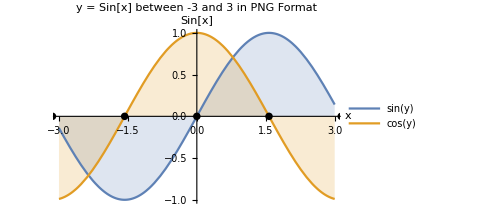

```mathematica
ClearAll[api,format]

api[fmt_String]:=APIFunction[
{
"a"->"Integer",
"b"->"Integer"
},
Function[
Framed@Plot[{Sin[y],Cos[y]},{y,#a,#b},
PlotLabel->Style[Framed["y = Sin[x] between "<>ToString[#a]<>" and "<>ToString[#b]<>" in "<>fmt<>" Format"],12,Black,Background->Lighter[LightGreen]],
Filling->Axis,
AxesLabel->{"x","Sin[x]"},
AxesStyle->{Directive[Thin,Dashed,Black],Blue},
PlotLegends->"Expressions",
Epilog->Flatten[{PointSize[0.015],Point[{#*Pi,0}]&/@Range[#a,#b,.5]}],
ImageSize->Medium
]
],
fmt];

format="PNG";
api[format][<|"a"->-3,"b"->3|>]
```

```mathematica
ClearAll[cd]
cd[fmt_String]:=CloudDeploy[
api[fmt],
"/live-coding/sin-"<>ToLowerCase[fmt]<>"/",
Permissions->"Public"
];
formats={"PNG","JPG","GIF","SVG"};
Table[cd[f],{f,formats}]
```

{CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/sin-png],CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/sin-jpg],CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/sin-gif],CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/sin-svg]}

```mathematica
ClearAll[url,session]
url=URLBuild[cd[format],<|"a"->-3,"b"->3|>]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/sin-png?a=-3&b=3

#### JPG

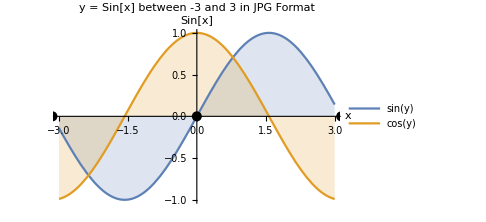

```mathematica
ClearAll[api,format]
format="JPG";
api=APIFunction[
{
"a"->"Integer",
"b"->"Integer"
},
Function[
Framed@Plot[{Sin[y],Cos[y]},{y,#a,#b},
PlotLabel->Style[Framed["y = Sin[x] between "<>ToString[#a]<>" and "<>ToString[#b]<>" in "<>format<>" Format"],12,Black,Background->Lighter[LightGreen]],
Filling->Axis,
AxesLabel->{"x","Sin[x]"},
AxesStyle->{Directive[Thin,Dashed,Black],Blue},
PlotLegends->"Expressions",
Epilog->{PointSize[0.02],Point[{-Pi,0}],Point[{0,0}],Point[{Pi,0}],Point[{2Pi,0}]},
ImageSize->Medium]
],
format];
api[<|"a"->-3,"b"->3|>]
```

```mathematica
ClearAll[cd]
cd=CloudDeploy[
api ,
"/live-coding/sin-"<>ToLowerCase[format]<>"/",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/sin-jpg]

#### GIF

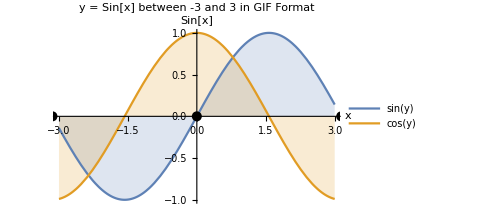

```mathematica
ClearAll[api,format]
format="GIF";
api=APIFunction[
{
"a"->"Integer",
"b"->"Integer"
},
Function[
Framed@Plot[{Sin[y],Cos[y]},{y,#a,#b},
PlotLabel->Style[Framed["y = Sin[x] between "<>ToString[#a]<>" and "<>ToString[#b]<>" in "<>format<>" Format"],12,Black,Background->Lighter[LightGreen]],
Filling->Axis,
AxesLabel->{"x","Sin[x]"},
AxesStyle->{Directive[Thin,Dashed,Black],Blue},
PlotLegends->"Expressions",
Epilog->{PointSize[0.02],Point[{-Pi,0}],Point[{0,0}],Point[{Pi,0}],Point[{2Pi,0}]},
ImageSize->Medium]
],
format];
api[<|"a"->-3,"b"->3|>]
```

```mathematica
ClearAll[cd]
cd=CloudDeploy[
api ,
"/live-coding/sin-"<>ToLowerCase[format]<>"/",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/sin-gif]

```mathematica
url=URLBuild[cd,<|"a"->-3,"b"->3|>]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/sin-gif?a=-3&b=3

#### SVG

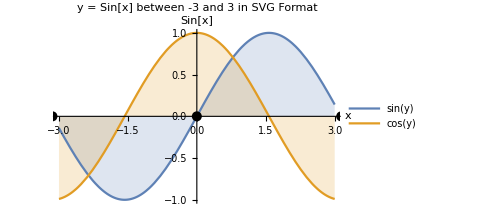

```mathematica
ClearAll[api,format]
format="SVG";
api=APIFunction[
{
"a"->"Integer",
"b"->"Integer"
},
Function[
Framed@Plot[{Sin[y],Cos[y]},{y,#a,#b},
PlotLabel->Style[Framed["y = Sin[x] between "<>ToString[#a]<>" and "<>ToString[#b]<>" in "<>format<>" Format"],12,Black,Background->Lighter[LightGreen]],
Filling->Axis,
AxesLabel->{"x","Sin[x]"},
AxesStyle->{Directive[Thin,Dashed,Black],Blue},
PlotLegends->"Expressions",
Epilog->{PointSize[0.02],Point[{-Pi,0}],Point[{0,0}],Point[{Pi,0}],Point[{2Pi,0}]},
ImageSize->Medium]
],
format];
api[<|"a"->-3,"b"->3|>]
```

```mathematica
ClearAll[cd]
cd=CloudDeploy[
api ,
"/live-coding/sin-"<>ToLowerCase[format]<>"/",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/mitch/live-coding/sin-svg]

```mathematica
ClearAll[url,session]
url=URLBuild[cd,<|"a"->-3,"b"->3|>]
session=StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/mitch/live-coding/sin-svg?a=-3&b=3